# Monte Carlo integration and the volume of N-Sphere

Jozsef Konczer

@ Milestone Institute

## Questions:

How can we use randomly generated numbers for Length, Area, Volume etc . calculation?

What is a random number?

How can we test the "quality" of random sources?

What is a suitable definitions of Cyrcle, Sphere, and N - Spheres?

How about Disk, Ball, and N - Balls?

## Definitions:

N-Sphere

N-Ball

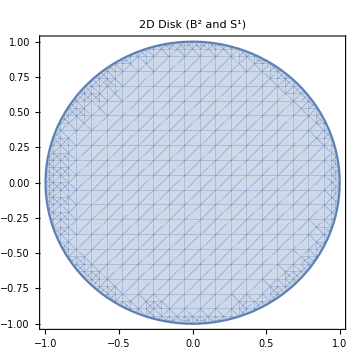

```mathematica
RegionPlot[x^2+y^2<1,
{x,-1,1},{y,-1,1},
PlotLabel->Style["2D Disk (B^2 and S^1)",16],

TicksStyle->Directive[Large,FontFamily->"Times",Italic],
PlotLabel->Style["2D Disk (B^2 and S^1)",16],
AxesStyle->{{Thick,Arrowheads[{0.0,0.05}]},{Thick,Arrowheads[{0.0,0.05}]}},
ImageSize->Medium
]
```

```mathematica
RegionPlot3D[x^2+y^2+z^2<=1,
{x,-1,1},{y,-1,1},{z,-1,1},
PlotStyle->Directive[Opacity[0.5]],Mesh->None,PlotPoints->50,

TicksStyle->Directive[Medium,FontFamily->"Times",Italic],
PlotLabel->Style["3D Ball (B^3 and S^2)",16],
ImageSize->Medium
]
```

-Graphics3D-

### Area and Chance

```mathematica
n=10000;

(*SeedRandom[2022(*,Method->"ExtendedCA"*)]*)
randomL=RandomReal[{-1,1},{n,2}];

Short[randomL]
```

{{0.124744,-0.385821},{0.745074,0.35025},«9997»,{0.3449,0.253127}}

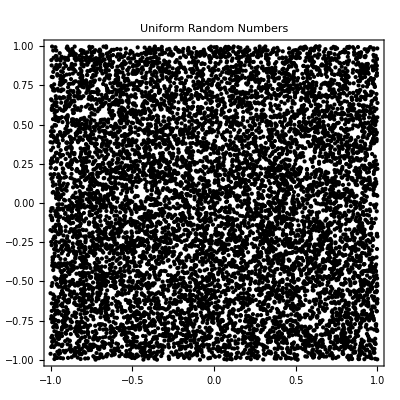

```mathematica
Graphics[Point[randomL],
PlotRange->{{-1,1},{-1,1}},

Frame->True,
PlotLabel->Style["Uniform Random Numbers",16],
TicksStyle->Directive[Medium,FontFamily->"Times",Italic]]
```

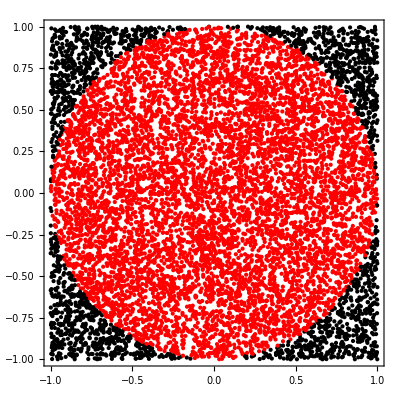

```mathematica
relation[{x_,y_}]:=x^2+y^2<=1

Graphics[{If[relation[#],Red,Black],Point[#]}&/@randomL,
PlotRange->{{-1,1},{-1,1}},
Frame->True
]
```

```mathematica
Short[{If[relation[#],Red,Black],Point[#]}&/@randomL]
```

## Abstraction:

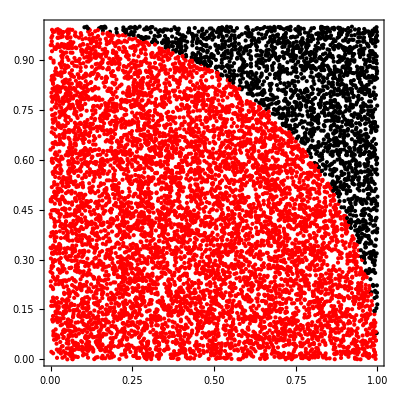

```mathematica
n=10000;

(*SeedRandom[2022(*,Method->"ExtendedCA"*)]*)
randomL=RandomReal[{0,1},{n,2}];

Graphics[{If[#.#<1,Red,Black],Point[#]}&/@randomL,PlotRange->{{0,1},{0,1}},Frame->True]
```

```mathematica
n=10000;

(*SeedRandom[2022(*,Method->"ExtendedCA"*)]*)
randomL=RandomReal[{0,1},{n,3}];

Graphics3D[{If[#.#<1,Red,Black],Point[#]}&/@randomL,PlotRange->{{0,1},{0,1},{0,1}}]
```

-Graphics3D-

#### Extra visualization:

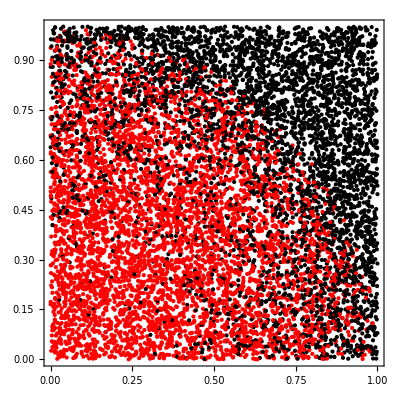

```mathematica
n=10000;

(*SeedRandom[2022(*,Method->"ExtendedCA"*)]*)
randomL=RandomReal[{0,1},{n,3}];

Graphics[{If[#.#<1,Red,Black],Point[#[[;;2]]]}&/@randomL,PlotRange->{{0,1},{0,1}},Frame->True]
```

```mathematica
n=10000;
(*SeedRandom[2022(*,Method->"ExtendedCA"*)]*)
randomL=RandomReal[{0,1},{n,12}];
Manipulate[
Graphics[{If[#[[;;d]].#[[;;d]]<1,Red,Black],Point[#[[;;2]]]}&/@randomL,PlotRange->{{0,1},{0,1}},Frame->True]
,{d,2,10,1}]
```

```mathematica
n=10000;
(*SeedRandom[2022(*,Method->"ExtendedCA"*)]*)
randomL=RandomReal[{0,1},{n,12}];

Manipulate[
Graphics3D[{If[#[[;;d]].#[[;;d]]<1,Red,Black],Point[#[[;;3]]]}&/@randomL,PlotRange->{{0,1},{0,1},{0,1}}]
,{d,3,10,1}]
```

## Computation:

```mathematica
n=10000;
randomL=RandomReal[{0,1},{n,2}];
```

```mathematica
4 N[Count[randomL,_?(#.#<1&)]/n]
```

3.1464

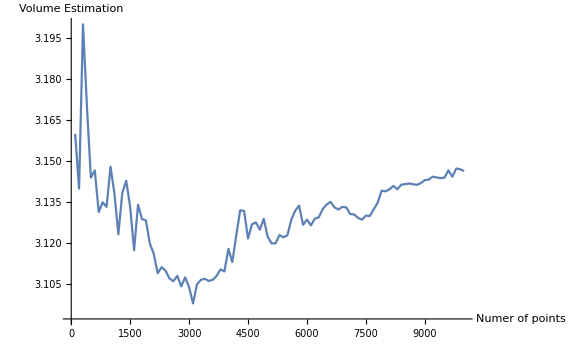

```mathematica
ListLinePlot[Table[{k,4 N[Count[randomL[[;;k]],_?(#.#<1&)]/k]},{k,100,n,100}],
PlotRange->All,
TicksStyle->Directive[Medium,FontFamily->"Times",Italic], 
AxesLabel->{"Numer of points","Volume Estimation"},
ImageSize->Large]
```

```mathematica
fMC[n_]:=N[Count[RandomReal[{0,1},{n,2}],_?(#.#<1&)]/n]
fMCVolume[n_]:=4 N[Count[RandomReal[{0,1},{n,2}],_?(#.#<1&)]/n]
```

```mathematica
n=1000000;
Text[Style["The result after " <>ToString[n]<>" samples is: "<>ToString[fMCVolume[1000000]],FontSize->80]]
```

The result after 1000000 samples is: 3.14302

### Generalization to d-Dimensions

```mathematica
fMC[n_,d_]:= N[Count[RandomReal[{0,1},{n,d}],_?(#.#<1&)]/n]
fMCVolume[n_,d_]:=2^d N[Count[RandomReal[{0,1},{n,d}],_?(#.#<1&)]/n]
```

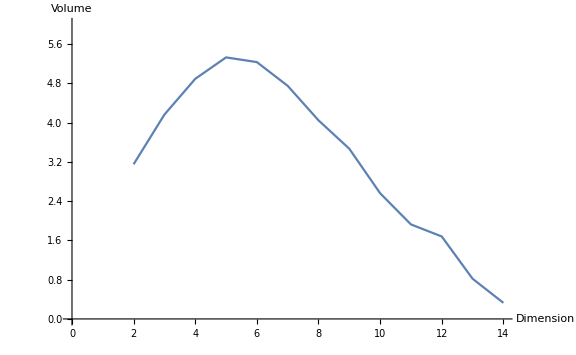

```mathematica
ListLinePlot[Table[{d,fMCVolume[100000,d]},{d,2,14}],
PlotRange->{0,6},ImageSize->Large,AxesLabel->{"Dimension","Volume"}]
```

## Interpretation:

The main feature (or bug) of Monte Carlo Integration, is that the result is not deterministic.

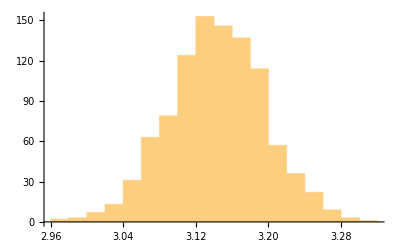

```mathematica
Histogram[Table[fMCVolume[1000],{k,1,1000}]]
```

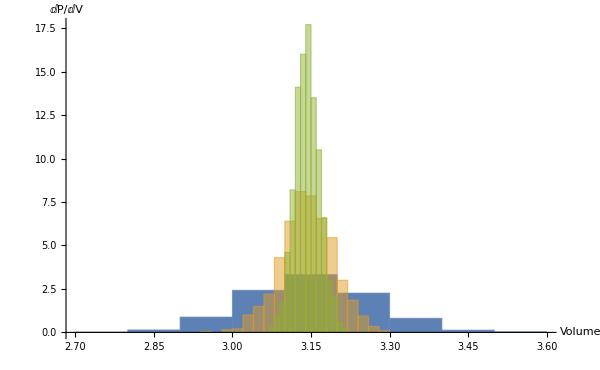

```mathematica
Show[
Histogram[Table[fMCVolume[200],{k,1,1000}],Automatic,"PDF",PlotRange->All,ChartStyle->ColorData[97,1]],
Histogram[{Table[fMCVolume[1000],{k,1,1000}]},Automatic,"PDF",PlotRange->All,ChartStyle->ColorData[97,2]],
Histogram[{Table[fMCVolume[5000],{k,1,1000}]},Automatic,"PDF",PlotRange->All,ChartStyle->ColorData[97,3]],
AxesLabel->{"Volume","ⅆP/ⅆV"}
]
```

### Central Limit Theorem

```mathematica
BernoulliDistribution[p]
```

```mathematica
Manipulate[
DiscretePlot[PDF[BernoulliDistribution[p],x]//Evaluate,{x,0,1},AxesOrigin->{1/2,0},PlotMarkers->Automatic,PlotRange->{0,1}]
,{{p,1/2},0,1}]
```

```mathematica
Manipulate[
Show[
Histogram[Table[Mean[RandomVariate[BernoulliDistribution[p],n]],{k,1,1000}],Automatic,"PDF"],
With[{m=p,σ=(n(1-p) p)^(1/2)/n},
Plot[1/((2 π)^(1/2)σ)ⅇ^(-(x-m)^2/(2 σ^2))//Quiet,{x,0,1},PlotRange->All]
]
,AxesLabel->{"Mean of n points","(ⅆ P)/(ⅆ m)"}
]
,{{n,100},1,5000,10},{{p,1/2},0,1}]
```

## Questions II

How can we quantify these uncertainties?

How the uncertainties depend on sample size and dimension?

What can we say about N-Ball volumes?

## Abstraction II

```mathematica
MCVolumeData=Table[fMCVolume[1000],{k,1,1000}];
Mean[MCVolumeData]
StandardDeviation[MCVolumeData]
```

3.14127

0.0514961

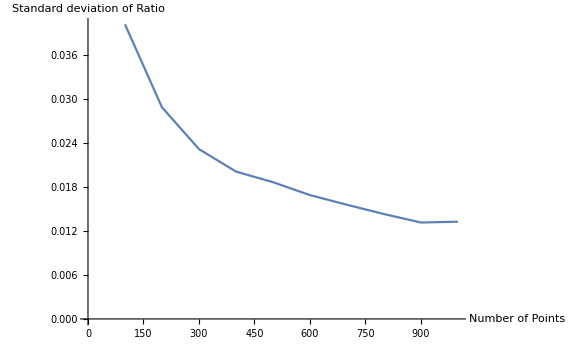

```mathematica
ListLinePlot[Table[{n,StandardDeviation[Table[fMC[n],{k,1,1000}]]},{n,100,1000,100}],AxesLabel->{"Number of Points","Standard deviation of Ratio"},ImageSize->Large,PlotRange->{0,All}]
```

```mathematica
NonlinearModelFit[Table[{n,StandardDeviation[Table[fMC[n],{k,1,1000}]]},{n,100,1000,100}],a Ν^α,{a,α},Ν]
```

FittedModel[0.42638/Ν^0.507771]

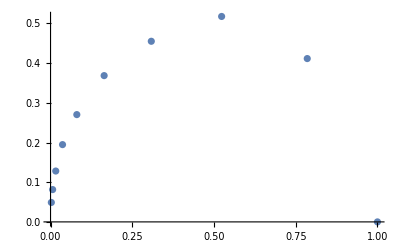

```mathematica
n=1000;
ListPlot[
MeanStandardDeviationList=Table[
With[
{data=Table[fMC[n,d],{k,1,1000}]},
{Mean[data],√n StandardDeviation[data]}
],{d,1,10}
]
]
```

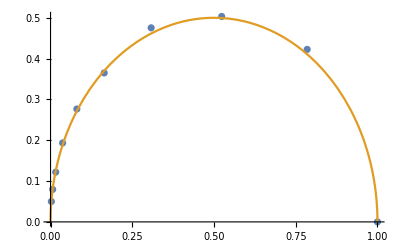

```mathematica
Show[
ListPlot[MeanStandardDeviationList],
Plot[(p(1-p))^(1/2),{p,0,1},PlotStyle->ColorData[97,2]]
]
```

## Computation II

```mathematica
∫_-z^z 1/(2 π)^(1/2)ⅇ^(-x^2/2)ⅆx
```

Erf[z/(√2)]

```mathematica
Solve[Erf[z/(√2)]==p,z]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{z→√2 InverseErf[p]}}

```mathematica
fMCVolume[n_,d_,p_]:=Module[
{ratio},
ratio=N[Count[RandomReal[{0,1},{n,d}],_?(#.#<1&)]/n];
Around[2^d ratio,2^d √2 InverseErf[p] (ratio(1-ratio))^(1/2)/n^(1/2) ]
]
```

```mathematica
fMCVolume[1000,3,0.99]
```

4.090.33

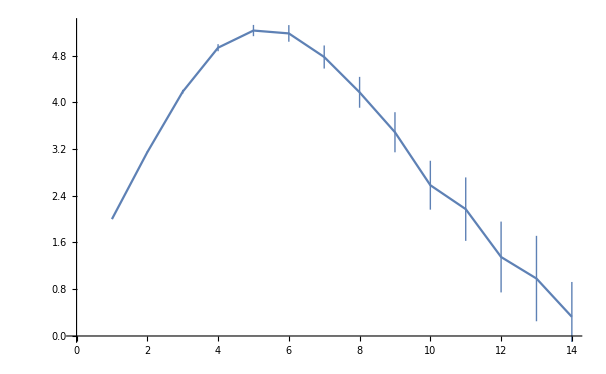

```mathematica
ListLinePlot[Table[{d,fMCVolume[100000,d,0.99]},{d,1,14}],PlotRange->{0,All}]
```

## Interpretation II

```mathematica
exactVolume[d_]:=π^(d/2)/Gamma[d/2+1]
```

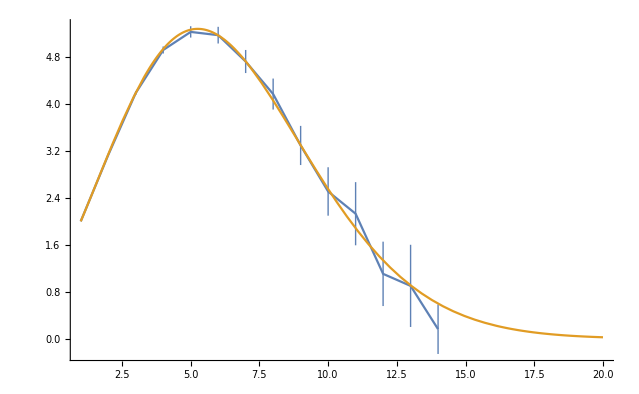

```mathematica
Show[
ListLinePlot[Table[{d,fMCVolume[100000,d,0.99]},{d,1,14}],PlotRange->{0,All}],
Plot[exactVolume[d],{d,1,20},PlotStyle->ColorData[97,2]],
PlotRange->All
]
```

## Conclusion (so far):

Monte Carlo Integration can be an informative Numerical method, if it is extended by error estimation.

## Remaining Questions:

How the random numbers are generated?

How the method can be extended?

Is there a Bayesian interpretation of the method?

How to speed up the simulation?

### Speeding up by Compiling:

```mathematica
cfMC=Compile[{{n, _Integer},{d,_Integer}},
 Module[
{s = 0}, 
Do[
If[(Total[RandomReal[{0,1},d]^2])<=1,
s++
],
{i,n}]; 
s/n],
RuntimeOptions->"Speed"]
```

CompiledFunction[…]

```mathematica
cfMC2=Compile[{{n, _Integer},{d,_Integer}},
 Module[
{rList},
rList=RandomReal[{0,1},{n,d}];
Total[Map[Boole[#.#<1]&,rList]]/n
]
,RuntimeOptions->"Speed"]
```

CompiledFunction[…]

```mathematica
AbsoluteTiming[cfMC[1000000,2]]
```

{0.152844,0.785051}

```mathematica
AbsoluteTiming[cfMC2[100000,2]]
```

{0.015435,0.78295}

```mathematica
cfMCVolume[n_Integer,d_Integer,p_]:=Module[
{ratio},
ratio=cfMC2[n,d];
Around[2^d ratio,2^d √2 InverseErf[p] (ratio(1-ratio))^(1/2)/n^(1/2) ]
]
```

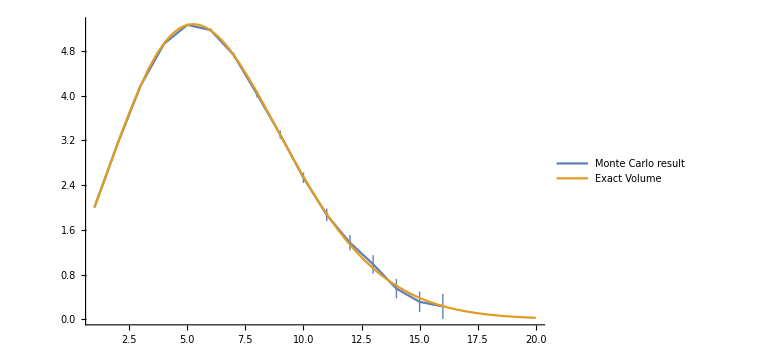

```mathematica
Show[
ListLinePlot[Table[{d,cfMCVolume[2000000,d,0.99]},{d,1,16}],PlotRange->{0,All},PlotLegends->{"Monte Carlo result"}],
Plot[exactVolume[d],{d,1,20},PlotStyle->ColorData[97,2],PlotLegends->{"Exact Volume"}],
PlotRange->All,
ImageSize->Large
]
```

## References and Resources

Monte Carlo Integration on  MIT OpenCourseWare:

https://www.youtube.com/watch?v=OgO1gpXSUzU&list=PLUl4u3cNGP619EG1wp0kT-7rDE_Az5TNd&index=6

Wikipedia article on Monte Carlo integration:

https://en.wikipedia.org/wiki/Monte_Carlo_integration

Wikipedia article on Volume of an N-Ball:

https://en.wikipedia.org/wiki/Volume_of_an_n-ball

Blog posts on Monte Carlo Integration:

https://www.cantorsparadise.com/demystifying-monto-carlo-integration-7c9bd0e37689

https://towardsdatascience.com/the-basics-of-monte-carlo-integration-5fe16b40482d